```mathematica
mn = 0.939;

μ[mx_]:=mx/mn;
γ[ve_]:= 1/Sqrt[1 - ve^2]; (*natural units *)
p[ve_, mx_]:=γ[ve]*mx*ve;
s[mx_] :=mx^2/μ[mx]^2*(1+μ[mx]^2+2/(√0.3)*μ[mx])(*2γ[ve]*mx*mn+mx^2+mn^2*);
Er[ctheta_,ve_, mx_]:= (mn*mx^2*γ[ve]^2*ve^2)/(mn^2 + mx^2 + 2*γ[ve]*mx*mn)*(1 - ctheta);
```

```mathematica
σTot[dσ_, mx_]:= Integrate[dσ[t,mx]* 0.3*((1+μ[mx]^2+2/(√0.3)*μ[mx])/(2*(1-0.3)*mx^2)),{t,0, 4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx])))}];
```

## Differential Cross Sections

```mathematica
d1[t_,mx_]:= (mn^2*(4*mx^2-t)*(4*mx^2-μ[mx]^2*t))/(32*π*(μ[mx])^2*s[mx]);
d2[t_,ve_, mx_]:= (mn^2*t*(μ[mx]^2*t - 4*mx^2))/(32*π*s[ve, mx]);
d3[t_,ve_, mx_]:= (mn^2*t*(t - 4*mx^2))/(32*π*s[ve, mx]);
d4[t_,ve_, mx_]:= (mn^2*t^2)/(32*π*s[ve, mx]);
d5[t_,ve_, mx_]:= (2*(μ[mx]^2+1)^2*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*s[ve, mx]*mx^2+μ[mx]^4*(2*s[ve, mx]^2+2*s[ve, mx]*t+t^2))/(16*π*μ[mx]^4*s[ve, mx]);
d6[t_,ve_, mx_]:= 1/(16*π*μ[mx]^4*s)(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[ve, mx] +s[ve, mx]+μ[mx]^2*t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[ve, mx]^2+2*s[ve, mx]*t+t^2));
d7[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[ mx] +s[ mx]+t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2));
```

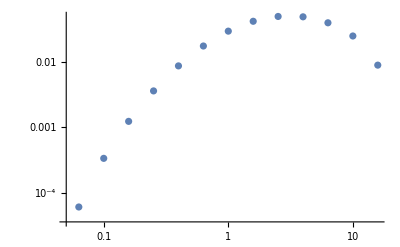

```mathematica
list = With[{x := 10^xp}, Table[{x,σTot[d1, x]}, {xp, -6, 6, 0.2}]];
ListLogLogPlot[list]
```

```mathematica
Table[Integrate[t^n, {t,  0, tm}], {n, 0, 2, 1}]
```

{tm,tm^2/2,tm^3/3}

{{1.×10^-6,-1.87105×10^-13},{1.58489×10^-6,-4.69984×10^-13},{2.51189×10^-6,-1.18053×10^-12},{3.98107×10^-6,-2.96532×10^-12},{6.30957×10^-6,-7.44836×10^-12},{0.00001,-1.87087×10^-11},{0.0000158489,-4.69912×10^-11},{0.0000251189,-1.18025×10^-10},{0.0000398107,-2.96418×10^-10},{0.0000630957,-7.44384×10^-10},{0.0001,-1.86907×10^-9},{0.000158489,-4.69196×10^-9},{0.000251189,-1.1774×10^-8},{0.000398107,-2.95285×10^-8},{0.000630957,-7.39879×10^-8},{0.001,-1.85118×10^-7},{0.00158489,-4.62099×10^-7},{0.00251189,-1.14931×10^-6},{0.00398107,-2.84207×10^-6},{0.00630957,-6.9642×10^-6},{0.01,-0.0000168211},{0.0158489,-0.0000397179},{0.0251189,-0.0000904938},{0.0398107,-0.000194928},{0.0630957,-0.000384197},{0.1,-0.000655264},{0.158489,-0.000860852},{0.251189,-0.000552362},{0.398107,0.000997898},{0.630957,0.00420464},{1.,0.0080017},{1.58489,0.00907446},{2.51189,0.00294061},{3.98107,-0.0130733},{6.30957,-0.0374792},{10.,-0.0654665},{15.8489,-0.0919662},{25.1189,-0.113908},{39.8107,-0.130468},{63.0957,-0.142206},{100.,-0.150188},{158.489,-0.155471},{251.189,-0.158908},{398.107,-0.161119},{630.957,-0.162531},{1000.,-0.163429},{1584.89,-0.163998},{2511.89,-0.164358},{3981.07,-0.164586},{6309.57,-0.16473},{10000.,-0.164821},{15848.9,-0.164878},{25118.9,-0.164914},{39810.7,-0.164937},{63095.7,-0.164952},{100000.,-0.164961},{158489.,-0.164966},{251189.,-0.16497},{398107.,-0.164972},{630957.,-0.164974},{1.×10^6,-0.164975}}

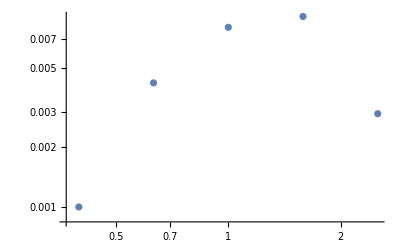

```mathematica
list2 = With[{x := 10^xp}, Table[{x,d1[4*x^2*((1-0.3)/(0.3*(1+μ[x]^2+2/(√0.3)*μ[x]))),x]}, {xp, -6, 6, 0.2}]]
ListLogLogPlot[list2]
```